20000

True

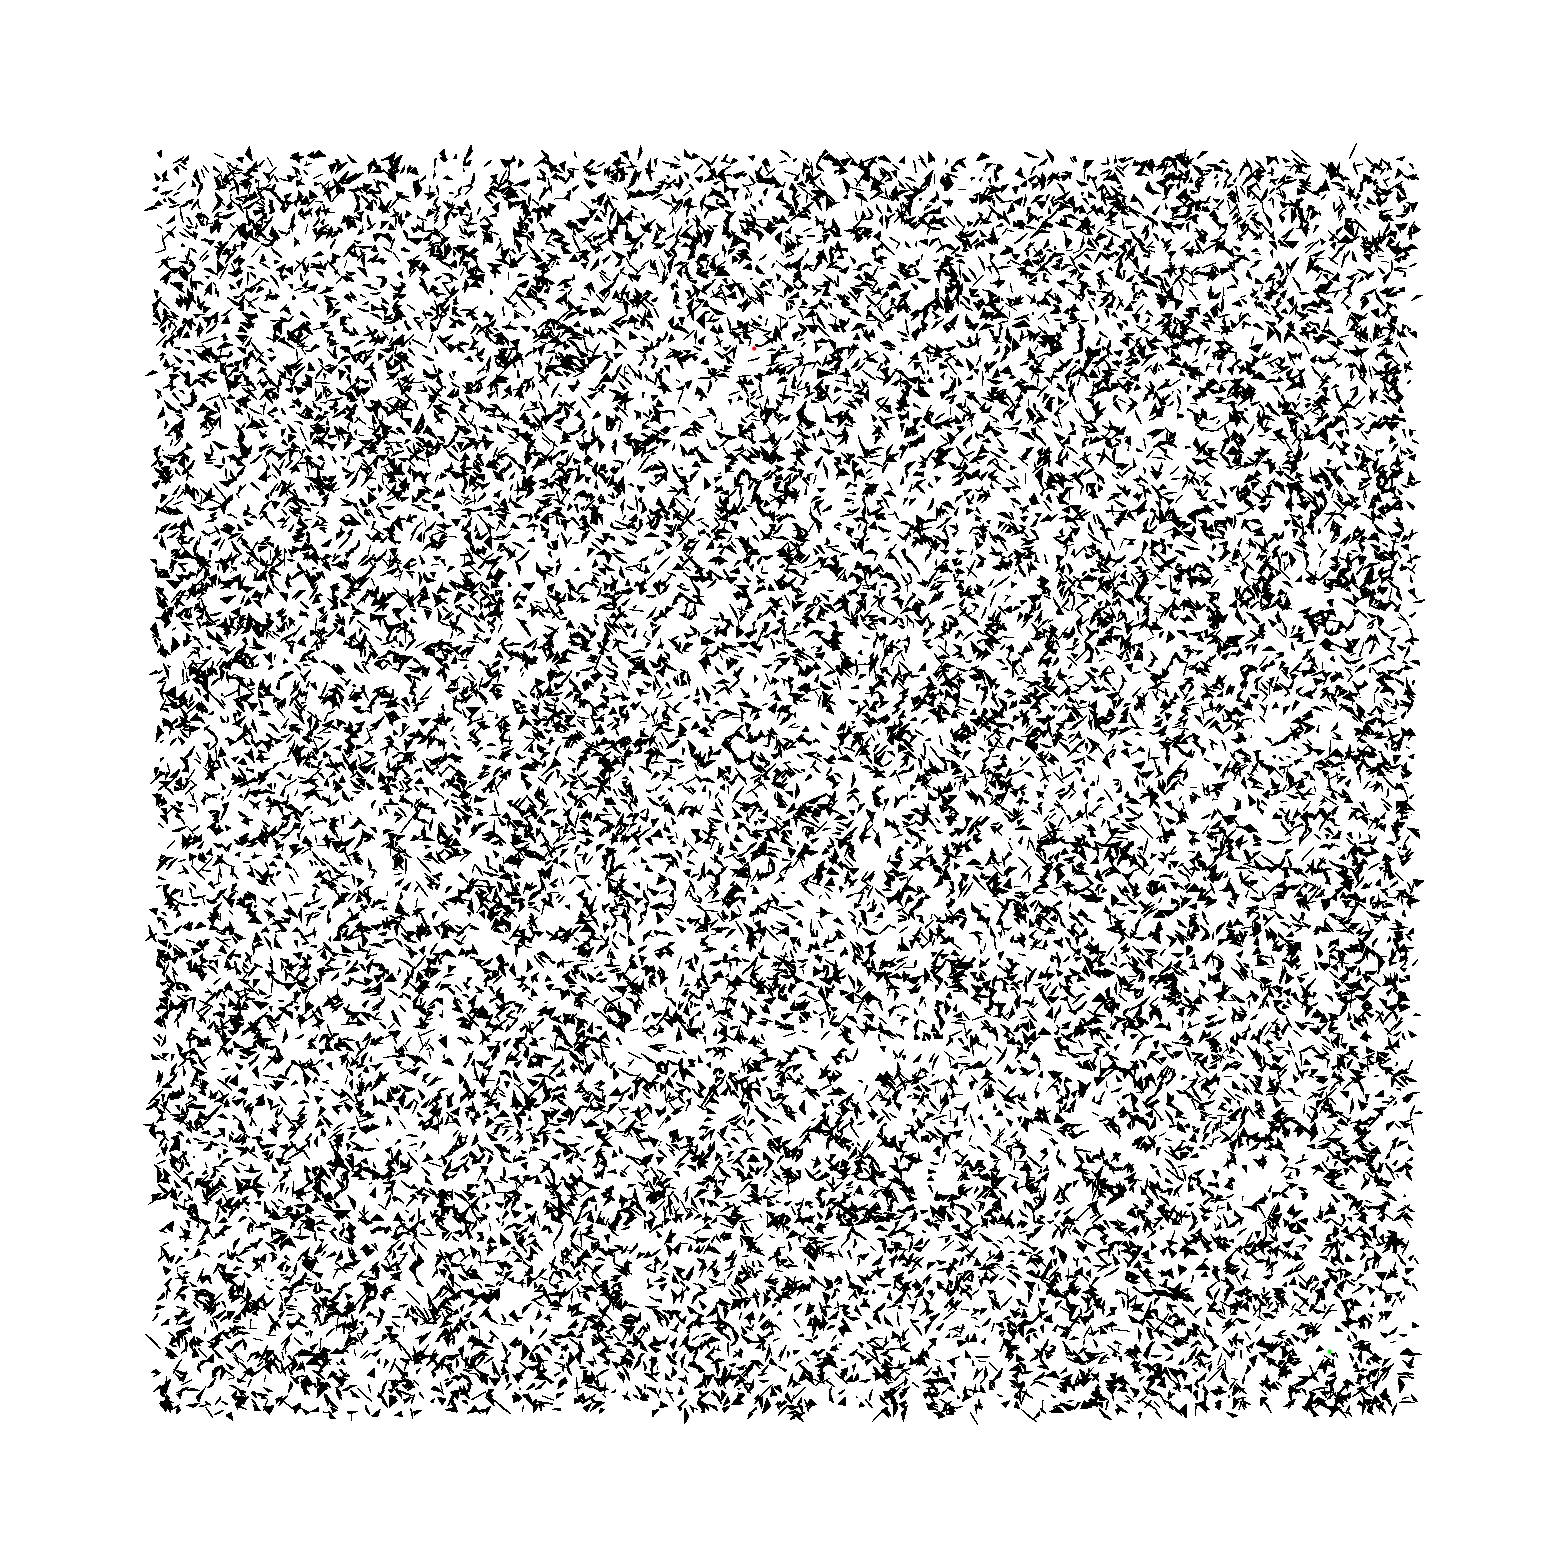

-Graphics-

```mathematica
ClearAll[Evaluate[Context[]<>"*"]]
SetDirectory[NotebookDirectory[]];
file=Import["input_4.txt","Table"];
numObstacles=file[[2,1]]
obstacles=Map[Partition[#,2]&,file[[3;;]]];
Length@obstacles==numObstacles
startPoint=First@Partition[file[[1]],2];
endPoint=Last@Partition[file[[1]],2];
Graphics[{Triangle@obstacles,PointSize[Large],Red,Point@startPoint,Green,Point@endPoint}]
Graphics[{
SelectFirst[Triangle/@obstacles,Element[startPoint,#]&,Null],
SelectFirst[Triangle/@obstacles,Element[endPoint,#]&,Null],
PointSize[Large],Red,Point@startPoint,Green,Point@endPoint}]
```

```mathematica
trigs=Triangle/@obstacles;
components={};
For[i=1,i<100,i++,
pos=FirstPosition[components,r_/;RegionDimension[RegionIntersection[r,trigs[[i]]]]>0,-1];
If[pos≠-1,components[[pos]]=RegionIntersection[components[[pos]],trigs[[i]]],AppendTo[components,trigs[[i]]]]
]
Length@components
```

99

```mathematica
components
```

{Triangle[{{5894,3426},{5977,3396},{5996,3297}}],Triangle[{{2730,8081},{2826,8173},{2858,8107}}],Triangle[{{2930,-246},{2988,-206},{2902,-255}}],Triangle[{{-52,3616},{-35,3583},{-129,3530}}],Triangle[{{41,2167},{9,2080},{-8,1982}}],Triangle[{{8610,7623},{8640,7579},{8654,7663}}],Triangle[{{-4883,7722},{-4926,7734},{-4880,7812}}],Triangle[{{5536,-4984},{5527,-5032},{5471,-5065}}],Triangle[{{8081,9013},{8125,9009},{8202,9105}}],Triangle[{{45,6517},{79,6558},{100,6491}}],Triangle[{{-4001,2468},{-3947,2498},{-3881,2531}}],Triangle[{{-2828,7772},{-2928,7779},{-2929,7740}}],Triangle[{{-3545,-76},{-3506,-93},{-3481,-81}}],Triangle[{{6325,5445},{6317,5460},{6373,5424}}],Triangle[{{6274,9916},{6370,9933},{6305,9912}}],Triangle[{{1743,1139},{1810,1067},{1825,1094}}],Triangle[{{997,334},{1056,264},{1054,183}}],Triangle[{{3137,-2707},{3185,-2639},{3110,-2615}}],Triangle[{{-3066,7592},{-3013,7515},{-3025,7576}}],Triangle[{{-1876,-1138},{-1798,-1225},{-1830,-1256}}],Triangle[{{7572,2415},{7657,2484},{7717,2460}}],Triangle[{{-248,1764},{-248,1719},{-321,1658}}],Triangle[{{1814,-63},{1823,-21},{1900,-81}}],Triangle[{{5890,1954},{5859,1921},{5950,2018}}],Triangle[{{3966,6562},{3902,6488},{3872,6399}}],Triangle[{{6415,2556},{6418,2567},{6489,2553}}],Triangle[{{395,1354},{448,1269},{388,1195}}],Triangle[{{1902,9346},{1846,9280},{1825,9264}}],Triangle[{{-2895,1799},{-2848,1703},{-2831,1715}}],Triangle[{{7616,5589},{7670,5585},{7768,5574}}],Triangle[{{8710,5060},{8795,4963},{8870,4947}}],Triangle[{{508,9825},{422,9764},{486,9707}}],Triangle[{{5171,-4613},{5206,-4622},{5242,-4677}}],Triangle[{{-408,7103},{-400,7130},{-440,7213}}],Triangle[{{6917,7171},{6984,7090},{6993,7001}}],Triangle[{{-3716,588},{-3775,612},{-3844,551}}],Triangle[{{-499,1260},{-540,1252},{-590,1330}}],Triangle[{{112,1668},{84,1624},{99,1557}}],Triangle[{{7624,4185},{7679,4210},{7624,4209}}],Triangle[{{106,9742},{203,9654},{165,9635}}],Triangle[{{303,3196},{248,3171},{289,3132}}],Triangle[{{8004,1169},{7994,1153},{7987,1181}}],Triangle[{{3580,-2192},{3554,-2145},{3454,-2228}}],Triangle[{{-3472,3440},{-3528,3482},{-3455,3530}}],Triangle[{{9688,7494},{9698,7426},{9667,7503}}],Triangle[{{9584,9403},{9620,9452},{9558,9454}}],Triangle[{{-1323,3321},{-1344,3394},{-1299,3304}}],Triangle[{{6026,965},{6058,967},{6111,876}}],Triangle[{{95,-3862},{195,-3880},{272,-3956}}],Triangle[{{3144,4206},{3052,4283},{3082,4339}}],Triangle[{{-235,-4564},{-181,-4515},{-252,-4553}}],Triangle[{{-2853,-2212},{-2755,-2288},{-2783,-2321}}],Triangle[{{2284,-2467},{2376,-2517},{2283,-2541}}],Triangle[{{-3137,1570},{-3138,1535},{-3172,1600}}],Triangle[{{7419,6473},{7461,6469},{7456,6498}}],Triangle[{{259,4749},{298,4797},{305,4862}}],Triangle[{{-2498,-4918},{-2507,-4958},{-2452,-5019}}],Triangle[{{4,9147},{36,9094},{120,9133}}],Triangle[{{-1985,4718},{-1993,4817},{-2010,4836}}],Triangle[{{-2949,6679},{-2852,6665},{-2942,6636}}],Triangle[{{4168,-4832},{4195,-4788},{4147,-4777}}],Triangle[{{3514,9058},{3479,9048},{3485,9017}}],Triangle[{{-834,9728},{-858,9689},{-781,9709}}],Triangle[{{-2555,-2175},{-2592,-2113},{-2672,-2183}}],Triangle[{{6683,7631},{6654,7611},{6611,7699}}],Triangle[{{1965,7881},{1926,7846},{1839,7900}}],Triangle[{{-426,1930},{-464,1980},{-470,1883}}],Triangle[{{1352,-1835},{1358,-1868},{1400,-1769}}],Triangle[{{8265,-3136},{8273,-3222},{8229,-3254}}],Triangle[{{7161,2972},{7222,2873},{7321,2832}}],Triangle[{{-496,461},{-458,397},{-376,318}}],Triangle[{{3879,4603},{3906,4698},{3817,4739}}],Triangle[{{9412,7708},{9317,7612},{9220,7680}}],Triangle[{{3126,2636},{3177,2577},{3085,2640}}],Triangle[{{9160,2797},{9241,2847},{9193,2858}}],Triangle[{{1392,8477},{1481,8396},{1449,8334}}],Triangle[{{9004,7230},{9094,7262},{9067,7278}}],Triangle[{{5218,5668},{5209,5743},{5175,5758}}],Triangle[{{-3758,-2475},{-3831,-2489},{-3749,-2520}}],Triangle[{{2558,3602},{2592,3687},{2555,3706}}],Triangle[{{2414,8520},{2449,8578},{2398,8603}}],Triangle[{{6477,-3269},{6405,-3332},{6308,-3372}}],Triangle[{{4092,7279},{4163,7181},{4086,7178}}],Triangle[{{-1889,-2898},{-1959,-2822},{-1918,-2835}}],Triangle[{{4616,-3948},{4634,-3970},{4587,-4063}}],Triangle[{{-633,-130},{-731,-107},{-712,-151}}],Triangle[{{6419,3406},{6451,3503},{6399,3504}}],Triangle[{{4250,-989},{4258,-956},{4275,-964}}],Triangle[{{-877,3264},{-884,3207},{-889,3190}}],Triangle[{{8182,6878},{8228,6884},{8203,6963}}],Triangle[{{2674,-2215},{2649,-2196},{2559,-2108}}],Triangle[{{8057,-3544},{7990,-3513},{8004,-3595}}],Triangle[{{-3217,4284},{-3308,4207},{-3261,4196}}],Triangle[{{7414,9638},{7398,9643},{7497,9743}}],Triangle[{{8653,4930},{8656,4996},{8581,4927}}],Triangle[{{6199,4137},{6248,4065},{6224,4056}}],Triangle[{{9427,8078},{9337,8049},{9253,8137}}],Triangle[{{5251,6290},{5183,6262},{5186,6311}}],Triangle[{{5501,3546},{5403,3589},{5414,3555}}]}

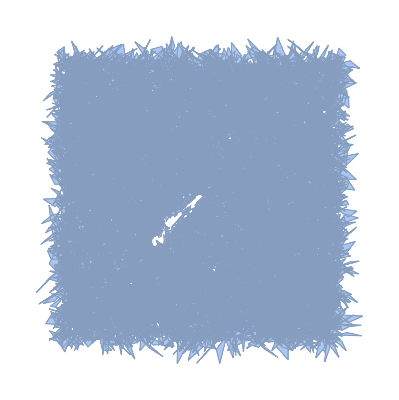

```mathematica
MeshRegion[Flatten[Map[Partition[#,2]&,file[[3;;]]],1],Triangle/@Partition[Range[numObstacles*3],3]]
```